```mathematica
MovingAverageTimeSeries[data:{{_,_}..},windowSize_Integer?Positive]:=Module[{times,values,ts,movingAvg},
(*Extract times and values from input data*)
{times,values}=Transpose[data];

(*Create a TimeSeries object for efficient temporal operations*)ts=TimeSeries[values,{times}];

(*Use MovingMap with Mean for the moving average calculation*)
(*"Fixed" partition ensures we only use available data within the window*)movingAvg=MovingMap[Mean,ts,windowSize,"Fixed"];

(*Return as {time,value} pairs*)
movingAvg["Path"]
]
```

```mathematica
MovingMap[Mean,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]},3]
```

{1/4 (x_1+x_2+x_3+x_4),1/4 (x_2+x_3+x_4+x_5)}

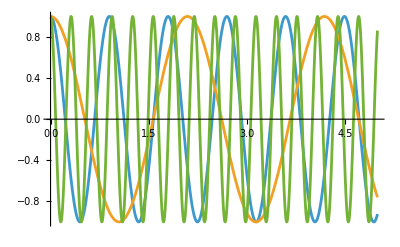

```mathematica
Plot[Re/@{Exp[-I*6.99*t],Exp[-I*3.*t],Exp[-I*20.*t]}//Evaluate,{t,0,5}]
```

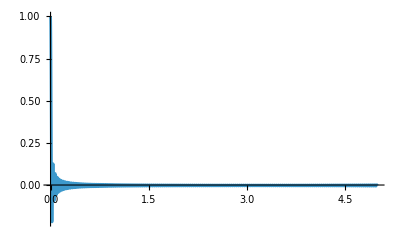

```mathematica
Plot[Total[Re[Exp[-I*#*t]]&/@Range[1,200,1.]]/200,{t,0,5},PlotRange->All]
```

```mathematica
Plot[Total[Re[Exp[-I*#*t]]&/@Range[1,200,1.]]/200,{t,0,5},PlotRange->All]
```

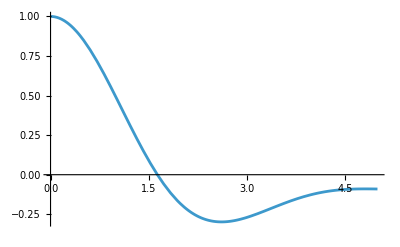

```mathematica
s=RandomVariate[RayleighDistribution[Sqrt[2/Pi]],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

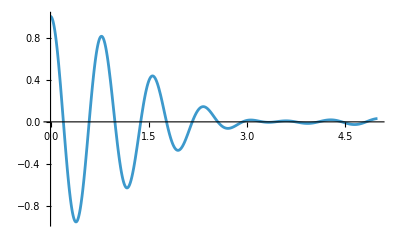

```mathematica
s=RandomVariate[NormalDistribution[8.,0.85],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

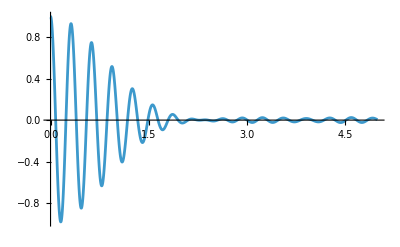

```mathematica
s=RandomVariate[NormalDistribution[20.,1.2],1000.];
Plot[Total[Cos[#*t]&/@s]/Length[s],{t,0,5},PlotRange->All]
```

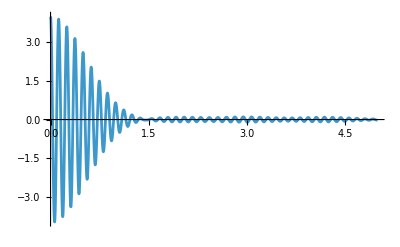

```mathematica
s1=RandomVariate[NormalDistribution[49.,1.5],1000.];
s2=RandomVariate[NormalDistribution[50.,1.5],1000.];
s3=RandomVariate[NormalDistribution[51.,1.5],1000.];
s4=RandomVariate[NormalDistribution[52.,1.5],1000.];
Plot[Total[Cos[#*t]&/@s1]/Length[s1]+Total[Cos[#*t]&/@s2]/Length[s2]+Total[Cos[#*t]&/@s3]/Length[s3]+Total[Cos[#*t]&/@s4]/Length[s4],{t,0,5},PlotRange->All]
```

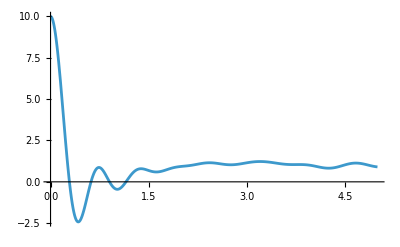

```mathematica
s=Flatten[RandomVariate[NormalDistribution[#,0.6+(#-2)*0.05],1000.]&/@Range[2,10]];
Plot[Total[Cos[#*t]&/@s]/1000.+1.,{t,0,5},PlotRange->All]
```

```mathematica
d=Table[Total[Cos[#*t]&/@s]/Length[s],{t,0,5,0.01}];
```

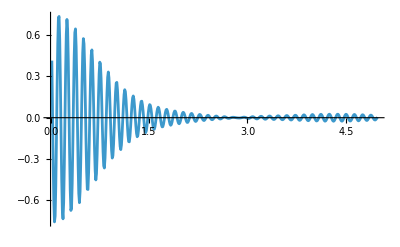

```mathematica
ListPlot[Transpose[{MovingMap[Mean,Range[0,5,0.01],4],MovingMap[Mean,d,4]}],Joined->True,PlotRange->All]
```

```mathematica
Needs["QMB`"]
```

```mathematica
e=Unfold[Sort@RandomReal[{-10,10},2000]]["UnfoldedLevels"];
```

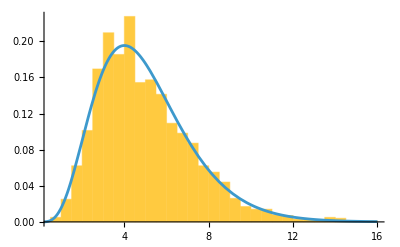

```mathematica
k=5;
Show[
Histogram[Differences[e,1,k],Automatic,"PDF"],
Plot[PDF[GammaDistribution[k,1],s],{s,0,16},PlotRange->All]
]
```

```mathematica
eigenvals=Unfold[Sort[Eigenvalues[RandomVariate[GaussianOrthogonalMatrixDistribution[4000]]]]]["UnfoldedLevels"];
```

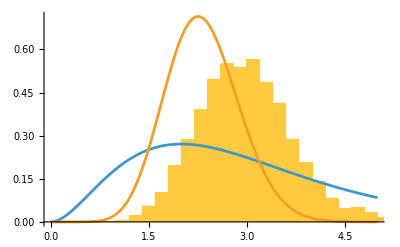

```mathematica
k=3;
Show[
Histogram[Differences[eigenvals,1,k],Automatic,"PDF",PlotRange->{{0,5},All}],
Plot[{PDF[GammaDistribution[k,1],s],GOESpacingDistribution[k,s]}//Evaluate,{s,0,5},PlotRange->All]
]
```

```mathematica
n=L=8;
J=1.;U=10.;(*chaotic regime*)
```

```mathematica
H=BoseHubbardHamiltonian[n,L,J,U,SymmetricSubspace->"EvenParity"];
energies=Unfold[Sort[Chop@Eigenvalues[Normal@H]]]["UnfoldedLevels"];
```

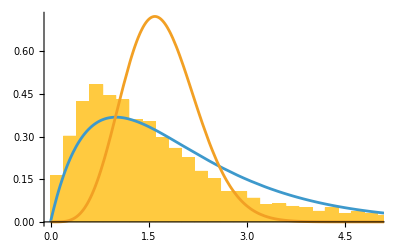

```mathematica
k=2;
Show[
Histogram[Differences[energies,1,k],Automatic,"PDF",PlotRange->{{0,5},All}],
Plot[{PDF[GammaDistribution[k,1],x],GOESpacingDistribution[k,x]}//Evaluate,{x,0,20},PlotRange->All]
]
```

```mathematica
FitPDF[data_List]:=Module[{dist,pdf},(*Step 1:Let Mathematica find the best-fitting distribution*)dist=FindDistribution[data];
(*Step 2:Define the PDF function*)pdf=PDF[dist,#]&;
<|"BestFitDistribution"->dist,"PDF"->pdf,"Mean"->Mean[dist],"Variance"->Variance[dist],"GoodnessOfFitTest"->DistributionFitTest[data,dist,"TestStatistic"],"PValue"->DistributionFitTest[data,dist,"PValue"]|>]
```

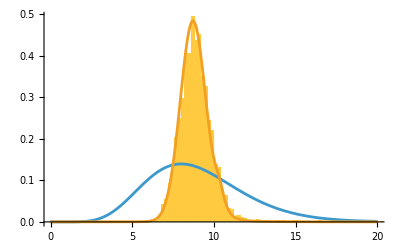

```mathematica
k=9;s=Differences[eigenvals,1,k];
fit=FitPDF[s];
Show[
Histogram[s,Automatic,"PDF",PlotRange->{{0,20},All}],
Plot[{PDF[GammaDistribution[k,1],x],fit["PDF"][x]}//Evaluate,{x,0,20},PlotRange->All]
]
```

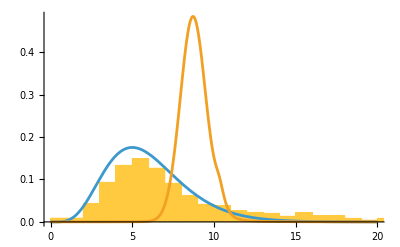

```mathematica
k=9;
Show[
Histogram[Differences[energies,1,k],Automatic,"PDF",PlotRange->{{0,20},All}],
Plot[{PDF[GammaDistribution[6,1],x],fit["PDF"][x]}//Evaluate,{x,0,20},PlotRange->All]
]
```